# Report Project 1

a) Poker: Hand probability - census method

## Summary

### Task

a) Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck of cards. The subset considered is cards valued 8,9,10,J,Q,K,A from the two decks.
Calculate the exact probability of the following hands using the  census method.

### Result

Let h(x) give the height as a function of distance x. The cross section area can be described as a function of height

A(h)=(10+2h) h

The requested volume to be transported away can thus be calculated with the following integral:

V=∫_0^2000 A(h(x))dx

The result is V≈101×10^3 m^3.

## Code

### Start

```mathematica
deckFinal = Sort[{108,109,110,111,112,113,114,108,109,110,111,112,113,114,
208,209,210,211,212,213,214,208,209,210,211,212,213,214
,308,309,310,311,312,313,314,308,309,310,311,312,313,314
,408,409,410,411,412,413,414,408,409,410,411,412,413,414}];
hands = Subsets[deckFinal,{5}];
```

### One Pair

```mathematica
pair0Q[{___,x_,x_,y_,y_,___}/;x≠y]:=False
pair0Q[{x_,x_,_,y_,y_}/;x≠y]:=False
pair0Q[{x_,x_,x_,y_,y_}/;x≠y]:=False
pair0Q[{x_,x_,y_,y_,y_}/;x≠y]:=False
pair0Q[{___,x_,x_,x_,x_,___}]:=False
pair0Q[{___,x_,x_,x_,___}]:=False
pair0Q[{___,x_,x_,___}]:=True
pair0Q[_]:=False
pair[hand_]:= pairQ[Sort[Mod[hand,100]]];
one = Count[hands,_?(pair)];
N[Count[hands,_?(pair)]/Length[hands]]*100"%"
```

### Two pair

```mathematica
twoPairProb[{x_,x_,x_,y_,y_}/;x≠y]:=False
twoPairProb[{x_,x_,y_,y_,y_}/;x≠y]:=False
twoPairProb[{___,x_,x_,y_,y_,___}/;x≠y]:=True
twoPairProb[{x_,x_,___,y_,y_}/;x≠y]:=True
twoPairProb[{___}]:=False
twoPair[hand_] :=twoPairProb[Sort[Mod[hand,100]]];
two = Count[hands,_?(twoPair)];
N[Count[hands,_?(twoPair)]/Length[hands]]*100"%"
```

### Three of a kind

```mathematica
threeProb[{x_,x_,x_,y_,y_}/;x≠y]:=False
threeProb[{x_,x_,y_,y_,y_}/;x≠y]:=False
threeProb[{___,x_,x_,x_,x_,___}]:=False
threeProb[{___,x_,x_,x_,___}]:=True
threeProb[{___}]:=False
threePair[hand_] :=threeProb[Sort[Mod[hand,100]]];
three= Count[hands,_?(threePair)];
N[Count[hands,_?(threePair)]/Length[hands]]*100"%"
```

### Four of a kind

```mathematica
fourProb[{___,x_,x_,x_,x_,___}]:=True
fourProb[{x_,x_,x_,x_,x_}]:=False
fourPair[hand_] :=fourProb[Sort[Mod[hand,100]]];
four= Count[hands,_?(fourPair)];
N[Count[hands,_?(fourPair)]/Length[hands]]*100"%"
```

### Five of a kind

```mathematica
fiveProb[{x_,x_,x_,x_,x_}]:=True
fivePair[hand_] :=fiveProb[Sort[Mod[hand,100]]];
five = Count[hands,_?(fivePair)];
N[Count[hands,_?(fivePair)]/Length[hands]]*100"%"
```

### Full house

```mathematica
fullProb[{x_,x_,x_,y_,y_}/;x≠y]:=True
fullProb[{x_,x_,y_,y_,y_}/;x≠y]:=True
fullPair[hand_] :=fullProb[Sort[Mod[hand,100]]];
full = Count[hands,_?(fullPair)];
N[Count[hands,_?(fullPair)]/Length[hands]]*100"%"
```

### Straight Flush

```mathematica
straightFlush[hand_]:=Sort[Mod[hand,100]]-Mod[Sort[Mod[hand,100]][[1]],100]=={0,1,2,3,4}&&Equal@@Quotient[hand,100];
straFlu = Count[hands,_?(straightFlush)];
N[Count[hands,_?(straightFlush)]/Length[hands]]*100"%"
```

### Straight

```mathematica
straight[hand_]:=(Sort[Mod[hand,100]]-Mod[Sort[Mod[hand,100]][[1]],100]=={0,1,2,3,4});
stra = Count[hands,_?(straight)];
N[(Count[hands,_?(straight)]-Count[hands,_?(straightFlush)])/Length[hands]]*100"%"
```

### Flush

```mathematica
flush[hand_]:=(!straightFlush[hand])&&Equal@@Quotient[hand,100]
flu = Count[hands,_?(flush)];
N[Count[hands,_?(flush)]/Length[hands]]*100"%"
```

### Nothing

```mathematica
nothing = Length[hands]- one-two-three-four-five-full-straFlu-stra-flu;
N[nothing/Length[hands]]*100"%"
```

b) Poker: Hand probability - combinatorial calculus

## Summary

### Task

Consider the following combinatorial calculus of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of seven possibilities {8,9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 48. The multiplication principle gives the result.

n_value=Binomial[7, 1],n_(4cards)=Binomial[8, 4], n_last=Binomial[48, 1]

n_4=n_value n_(4cards)n_last=Binomial[7, 1] Binomial[8, 4]Binomial[48, 1]

∴P_4=n_4/n_tot=(Binomial[7, 1] Binomial[8, 4]Binomial[48, 1])/Binomial[56, 5]=23520/3819816=140/22737≈0.00615736

Now, verify this probability by your census in part a).
Add combinatorial calculus for flush, straight, full house and 3 of a kind to your report. Also verify these calculations by your census.

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Code

```mathematica
ClearAll["`*"]

(* Verification of Four of a kind from census *)

(*Straight flush prob.*)
sFP = Binomial[4,1]*Binomial[3,1]*(Binomial[2,1]^5);
(*Total prob*)
sT = Binomial[56,5];
(* Flush *)
(*({{14}, {5}})({{4}, {1}}) - ({{4}, {1}})({{3}, {1}})({{2}, {1}})^5*)
Text["Flush"]
N[(((Binomial[14,5])*(Binomial[4,1])) -sFP )/(sT)]*100 "%"

(* Straight *)
(*({{3}, {1}})({{8}, {1}})^5 - ({{4}, {1}})({{3}, {1}})({{2}, {1}})^5*)
Text["Straight"]
N[((((Binomial[3,1])*(Binomial[8,1]^5)) - (sFP))/(sT))] *100 "%"

(* Full House *)
(*({{7}, {1}})({{8}, {3}})({{6}, {1}})({{8}, {2}})*)
Text["Full House"]
N[(Binomial[7,1]*Binomial[8,3]*Binomial[6,1]*(Binomial[8,2]))/(sT)]*100 "%"

(* Three of a kind*)
(*({{7}, {1}})({{8}, {3}})({{6}, {2}})({{8}, {1}})^2*)
Text["Three of a kind"]
N[(Binomial[7,1]*Binomial[8,3]*Binomial[6,2]*(Binomial[8,1]^2))/(sT)]*100 "%"
```

Flush

0.199591 %

Straight

2.56347 %

Full House

1.72406 %

Three of a kind

9.85178 %

c) One pair probability - Monte Carlo method

## Summary

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Result

The diagram clearly shows that the values converge towards a more stable probability with increased sample size.

## Code

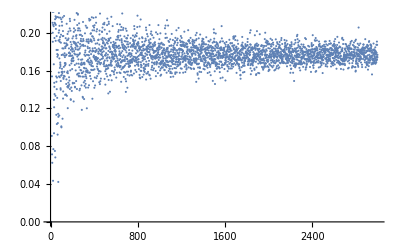

```mathematica
ClearAll["`*"]
(*Same deck from a), first int represents number, the next two represent 8-A*)
deck = {108,109,110,111,112,113,114,108,109,110,111,112,113,114,208,209,210,211,212,213,214,208,209,210,211,212,213,214,308,309,310,311,312,313,314,308,309,310,311,312,313,314,408,409,410,411,412,413,414,408,409,410,411,412,413,414};

hand := RandomSample[deck,5];
(*Conditionals from a to sort out the events where a pair occurs but are not stritcly a pair*) 
pairQ[{x_,x_,y_,y_}/;x≠y]:=False; (*Two pairs*)
pairQ[{___,x_,x_,x_,___}]:= False ;(*Three of a kind*)
pairQ[{___}]:=False; (*else*)
pairQ[{___,x_,x_,___}]:=True; (*Pair*)

(* Function suggestions from the project description with varying inputs of N according to the Monte Carlo method *)
ListPlot[Table[(Count[Sort/@Table[hand,{n}],_?(pairQ)])/n,{n,1,3000}]]
```